```mathematica
allGraphs5[k5Key,"parents"]
```

{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841}

```mathematica
allGraphs5[361,"colofourrealnull"]
```

-4 n1x2345+2 n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5

```mathematica
ChangeSymbol[s_]:=Symbol[StringReplace[SymbolName[s],"v"->"n"]]
```

```mathematica
Map[ChangeSymbol[#]&,allGraphs5[361,"colofour"]]
```

n12x35x4+n12x3x4x5+n135x2x4+n13x2x4x5+n14x2x35+n14x2x3x5+n15x2x3x4+n1x2x35x4+n1x2x3x4x5

```mathematica
MobiusGraphDouble5[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs5[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,6}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[TableForm[{Style[n,Bold,12,"Calibri",If[Coefficient[form3,n]==0,Black,Blue]],Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]},TableAlignments->Center],found[n,"graph"]],{Left}
],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Map[#->{Thick,Blue}&,edges2],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->800]
]
```

```mathematica
repBase5=Table[allGraphs5[k,"colofour"]->Labeled[Graph[allGraphs5[k,"graph"]],Style[allGraphs5[k,"colofour"],Blue,12],ImageSize->{50,50}],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→-Graphics-v1x2x3x4x5,v1x2x3x45→-Graphics-v1x2x3x45,v1x2x35x4→-Graphics-v1x2x35x4,v1x2x34x5→-Graphics-v1x2x34x5,v1x2x345→-Graphics-v1x2x345,v1x25x3x4→-Graphics-v1x25x3x4,v1x25x34→-Graphics-v1x25x34,v1x24x3x5→-Graphics-v1x24x3x5,v1x24x35→-Graphics-v1x24x35,v1x245x3→-Graphics-v1x245x3,v1x23x4x5→-Graphics-v1x23x4x5,v1x23x45→-Graphics-v1x23x45,v1x235x4→-Graphics-v1x235x4,v1x234x5→-Graphics-v1x234x5,v1x2345→-Graphics-v1x2345,v15x2x3x4→-Graphics-v15x2x3x4,v15x2x34→-Graphics-v15x2x34,v15x24x3→-Graphics-v15x24x3,v15x23x4→-Graphics-v15x23x4,v15x234→-Graphics-v15x234,v14x2x3x5→-Graphics-v14x2x3x5,v14x2x35→-Graphics-v14x2x35,v14x25x3→-Graphics-v14x25x3,v14x23x5→-Graphics-v14x23x5,v14x235→-Graphics-v14x235,v145x2x3→-Graphics-v145x2x3,v145x23→-Graphics-v145x23,v13x2x4x5→-Graphics-v13x2x4x5,v13x2x45→-Graphics-v13x2x45,v13x25x4→-Graphics-v13x25x4,v13x24x5→-Graphics-v13x24x5,v13x245→-Graphics-v13x245,v135x2x4→-Graphics-v135x2x4,v135x24→-Graphics-v135x24,v134x2x5→-Graphics-v134x2x5,v134x25→-Graphics-v134x25,v1345x2→-Graphics-v1345x2,v12x3x4x5→-Graphics-v12x3x4x5,v12x3x45→-Graphics-v12x3x45,v12x35x4→-Graphics-v12x35x4,v12x34x5→-Graphics-v12x34x5,v12x345→-Graphics-v12x345,v125x3x4→-Graphics-v125x3x4,v125x34→-Graphics-v125x34,v124x3x5→-Graphics-v124x3x5,v124x35→-Graphics-v124x35,v1245x3→-Graphics-v1245x3,v123x4x5→-Graphics-v123x4x5,v123x45→-Graphics-v123x45,v1235x4→-Graphics-v1235x4,v1234x5→-Graphics-v1234x5,v12345→-Graphics-v12345}

```mathematica
repBase4
```

{v1x2x3x4→-Graphics-v1x2x3x4,v1x2x34→-Graphics-v1x2x34,v1x24x3→-Graphics-v1x24x3,v1x23x4→-Graphics-v1x23x4,v1x234→-Graphics-v1x234,v14x2x3→-Graphics-v14x2x3,v14x23→-Graphics-v14x23,v13x2x4→-Graphics-v13x2x4,v13x24→-Graphics-v13x24,v134x2→-Graphics-v134x2,v12x3x4→-Graphics-v12x3x4,v12x34→-Graphics-v12x34,v124x3→-Graphics-v124x3,v123x4→-Graphics-v123x4,v1234→-Graphics-v1234}

```mathematica
SummaryPrint5[k_]:=With[
{g=MobiusGraphDouble5[k5Key,k,allGraphs5], gr=allGraphs5[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
g
}],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Style[ChromaticPolynomial[gr,3],Blue],
Style[StandardForm[((allGraphs5[k,"colofour"])/.repBase5)],Darker[Green],8]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

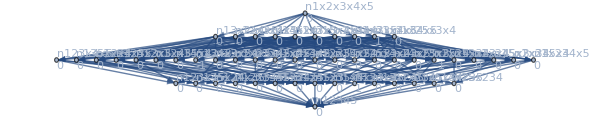
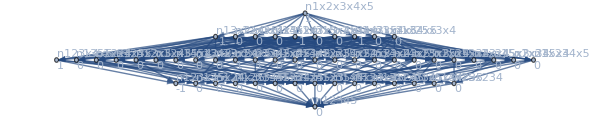
{-Graphics-8793-Graphics-n134x25-n134x2x5-n1x25x34+n1x2x34x5x^4-2 x^3+x^2
(x-1)^2 x^2
36
-Graphics-v12x345+-Graphics-v15x234+-Graphics-v12x34x5+-Graphics-v1x234x5+-Graphics-v15x2x34+-Graphics-v1x2x345+-Graphics-v1x2x34x5,-Graphics-6805-Graphics--n123x45+n123x4x5+n13x2x45-n13x2x4x5+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5x^5-3 x^4+3 x^3-x^2
(x-1)^3 x^2
72
-Graphics-v125x34+-Graphics-v124x35+-Graphics-v124x3x5+-Graphics-v12x34x5+-Graphics-v125x3x4+-Graphics-v12x35x4+-Graphics-v15x24x3+-Graphics-v14x25x3+-Graphics-v15x2x34+-Graphics-v1x25x34+-Graphics-v14x2x35+-Graphics-v1x24x35+-Graphics-v12x3x4x5+-Graphics-v14x2x3x5+-Graphics-v1x24x3x5+-Graphics-v1x2x34x5+-Graphics-v15x2x3x4+-Graphics-v1x25x3x4+-Graphics-v1x2x35x4+-Graphics-v1x2x3x4x5}

```mathematica
Table[
SummaryPrint5[k]
,{k,RandomSample[Keys[allGraphs5],2]}
]
```